```mathematica
(* BLOCK 1 - Definitions and initializations *)

Clear[a];

(* Assume all variables are real *)
(*$Assumptions=Element[t,Reals]&&Element[x,Reals]&&Element[y,Reals]&&Element[z,Reals]Element[x0[τ],Reals]&&Element[x1[τ],Reals]&&Element[x2[τ],Reals]&&Element[x3[τ],Reals]&&Element[p0[τ],Reals]&&Element[p1[τ],Reals]&&Element[p2[τ],Reals]&&Element[p3[τ],Reals]&&Element[s,Reals]&&Element[a,Reals]&&Element[r[x,y,z],Reals]&&r[x,y,z]>0;*)

(* Coordinates *)

(* X^μ *)
X={t,x,y,z};
Xτ={x0[τ],x1[τ],x2[τ],x3[τ]};

(* Subscript[P, μ] *)
P={p0,p1,p2,p3};

(* Subscript[P, i] *)
p={p1,p2,p3};
Pτ={p1[τ],p2[τ],p3[τ]};


(* KS coordinates for Kerr (t, x, y, z) = (x0, x1, x2, x3) *)

M=1;  (* mass *)
rs = 2M; (* Schwarzschild radius *)

L={1,(r[x,y,z] x+a y)/(r[x,y,z]^2+a^2),(r[x,y,z] y-a x)/(r[x,y,z]^2+a^2),z/r[x,y,z]};
Lu={-1,(r[x,y,z] x+a y)/(r[x,y,z]^2+a^2),(r[x,y,z] y-a x)/(r[x,y,z]^2+a^2),z/r[x,y,z]};
(*r=√((x^2+y^2+z^2-a^2+√((x^2+y^2+z^2-a^2)^2+4 a^2 z^2))/2);*)

(* Metric Subscript[g, μν] *)

g=({{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})+(2 M r[x,y,z]^3)/(r[x,y,z]^4+a^2 z^2)Table[L[[i]]L[[j]],{i,1,4},{j,1,4}]//FullSimplify;

(* Inverse metric g^μν *)

ig=({{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})-(2 M r[x,y,z]^3)/(r[x,y,z]^4+a^2 z^2)Table[Lu[[i]]Lu[[j]],{i,1,4},{j,1,4}]//FullSimplify;

(* Orthonormal tetrad (Subscript[d, a])^μ and dual tetrad Subscript[(e^a), μ], with (Subscript[d, a])^μ = t^μ *)

e0=({{1/(√(1+(2 M r[x,y,z]^3)/(r[x,y,z]^4+a^2 z^2)))}, {0}, {0}, {0}});
e1=({{(2 r[x,y,z]^3 (a y+x r[x,y,z]) (a^2+r[x,y,z]^2) √((a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4)/(a^2 z^2-2 z^2 r[x,y,z]+2 r[x,y,z]^3+r[x,y,z]^4)) √(1+(2 r[x,y,z]^3 (a x-y r[x,y,z])^2)/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))))/(√((a^4 z^2+2 (x^2+y^2) r[x,y,z]^3+r[x,y,z]^6+a^2 r[x,y,z]^2 (z^2+r[x,y,z]^2))/((a^2+r[x,y,z]^2) (a^2 z^2+r[x,y,z]^4+2 (-z^2 r[x,y,z]+r[x,y,z]^3)))) √(1+(2 r[x,y,z]^3)/(a^2 z^2+r[x,y,z]^4)) (a^6 z^2-4 a x y r[x,y,z]^4+2 y^2 r[x,y,z]^5+r[x,y,z]^8+a^2 r[x,y,z]^3 (2 x^2+z^2 r[x,y,z]+2 r[x,y,z]^3)+a^4 (2 z^2 r[x,y,z]^2+r[x,y,z]^4)))}, {((a^2+r[x,y,z]^2)^2 √((a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4)/(a^2 z^2-2 z^2 r[x,y,z]+2 r[x,y,z]^3+r[x,y,z]^4)) √((a^4 z^2+2 (x^2+y^2) r[x,y,z]^3+r[x,y,z]^6+a^2 r[x,y,z]^2 (z^2+r[x,y,z]^2))/((a^2+r[x,y,z]^2) (a^2 z^2+r[x,y,z]^4+2 (-z^2 r[x,y,z]+r[x,y,z]^3)))) (a^2 z^2+r[x,y,z]^4+2 (-z^2 r[x,y,z]+r[x,y,z]^3)) √(1+(2 r[x,y,z]^3 (a x-y r[x,y,z])^2)/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))))/(√(1+(2 r[x,y,z]^3)/(a^2 z^2+r[x,y,z]^4)) (a^6 z^2-4 a x y r[x,y,z]^4+2 y^2 r[x,y,z]^5+r[x,y,z]^8+a^2 r[x,y,z]^3 (2 x^2+z^2 r[x,y,z]+2 r[x,y,z]^3)+a^4 (2 z^2 r[x,y,z]^2+r[x,y,z]^4)))}, {0}, {(2 z r[x,y,z]^2 (a y+x r[x,y,z]) (a^2+r[x,y,z]^2) √((a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4)/(a^2 z^2-2 z^2 r[x,y,z]+2 r[x,y,z]^3+r[x,y,z]^4)) √(1+(2 r[x,y,z]^3 (a x-y r[x,y,z])^2)/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))))/(√((a^4 z^2+2 (x^2+y^2) r[x,y,z]^3+r[x,y,z]^6+a^2 r[x,y,z]^2 (z^2+r[x,y,z]^2))/((a^2+r[x,y,z]^2) (a^2 z^2+r[x,y,z]^4+2 (-z^2 r[x,y,z]+r[x,y,z]^3)))) √(1+(2 r[x,y,z]^3)/(a^2 z^2+r[x,y,z]^4)) (a^6 z^2-4 a x y r[x,y,z]^4+2 y^2 r[x,y,z]^5+r[x,y,z]^8+a^2 r[x,y,z]^3 (2 x^2+z^2 r[x,y,z]+2 r[x,y,z]^3)+a^4 (2 z^2 r[x,y,z]^2+r[x,y,z]^4)))}});
e2=({{(2 r[x,y,z]^3 (-a x+y r[x,y,z]))/((a^2+r[x,y,z]^2) (a^2 z^2+r[x,y,z]^4) √(1+(2 r[x,y,z]^3 (a x-y r[x,y,z])^2)/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))))}, {(2 r[x,y,z]^3 (a y+x r[x,y,z]) (-a x+y r[x,y,z]))/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4) √(1+(2 r[x,y,z]^3 (a x-y r[x,y,z])^2)/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))))}, {√(1+(2 r[x,y,z]^3 (a x-y r[x,y,z])^2)/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4)))}, {(2 z r[x,y,z]^2 (-a x+y r[x,y,z]))/((a^2+r[x,y,z]^2) (a^2 z^2+r[x,y,z]^4) √(1+(2 r[x,y,z]^3 (a x-y r[x,y,z])^2)/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))))}});
e3=({{(2 z r[x,y,z]^2 √((a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4)/(a^2 z^2+r[x,y,z]^4+2 (-z^2 r[x,y,z]+r[x,y,z]^3))))/(a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4)}, {0}, {0}, {√((a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4)/(a^2 z^2+r[x,y,z]^4+2 (-z^2 r[x,y,z]+r[x,y,z]^3)))}});
d0=(e0.ig)//Simplify;
d1=((r[x,y,z]^6+2 M r[x,y,z]^3 (x^2+y^2)+a^4 z^2+a^2 r[x,y,z]^2 (r^2+z^2))/((a^2+r[x,y,z]^2) (r[x,y,z]^4+a^2 z^2+2 M (r[x,y,z]^3-r[x,y,z] z^2))))^(-1/2)({{0}, {(√((a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4)/(z^2 (a^2-2 r[x,y,z])+r[x,y,z]^3 (2+r[x,y,z]))) √(1+(2 r[x,y,z]^3 (a x-y r[x,y,z])^2)/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))))/(√(1+(2 r[x,y,z]^3)/(a^2 z^2+r[x,y,z]^4)))}, {(2 r[x,y,z]^3 (a^2 x y+a (x^2-y^2) r[x,y,z]-x y r[x,y,z]^2) √((a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4)/(z^2 (a^2-2 r[x,y,z])+r[x,y,z]^3 (2+r[x,y,z]))) √(1+(2 r[x,y,z]^3 (a x-y r[x,y,z])^2)/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))))/(√(1+(2 r[x,y,z]^3)/(a^2 z^2+r[x,y,z]^4)) (a^6 z^2-4 a x y r[x,y,z]^4+2 y^2 r[x,y,z]^5+r[x,y,z]^8+a^2 r[x,y,z]^3 (2 x^2+z^2 r[x,y,z]+2 r[x,y,z]^3)+a^4 (2 z^2 r[x,y,z]^2+r[x,y,z]^4)))}, {0}});
d2=({{0}, {0}, {1/(√(1+(2 M r[x,y,z]^3 (a x-r y)^2)/((a^2+r[x,y,z]^2)^2 (r[x,y,z]^4+a^2 z^2))))}, {0}});
d3=(e3.ig)//Simplify; 
Td=e0;
T=d0;

Detg=-1;


(* Christoffel Subscript[Γ^i, jk] = 1/2 g^im( ∂_k Subscript[g, mj] + ∂_j Subscript[g, mk] - ∂_m Subscript[g, jk] ) *)

Γ=1/2 Parallelize[Table[(∑_(m=1)^4 (ig[[i]][[m]](D[g[[m]][[j]],X[[k]]]+D[g[[m]][[k]],X[[j]]]-D[g[[j]][[k]],X[[m]]])))//FullSimplify,{i,1,4},{j,1,4},{k,1,4}]];

(* Riemann Subscript[R^i, jkl] = ∂_k Subscript[Γ^i, lj] - ∂_l Subscript[Γ^i, kj] + Subscript[Γ^i, km] Subscript[Γ^m, lj] - Subscript[Γ^i, lm] Subscript[Γ^m, kj] *)

Riem=Table[(D[Γ[[i]][[l]][[j]],X[[k]]]-D[Γ[[i]][[k]][[j]],X[[l]]]+∑_(m=1)^4 (Γ[[i]][[k]][[m]]Γ[[m]][[l]][[j]]-Γ[[i]][[l]][[m]]Γ[[m]][[k]][[j]]))//Simplify,{i,1,4},{j,1,4},{k,1,4},{l,1,4}]//Parallelize;
(* Riemann Subscript[R, ijkl] *)
(*R=Table[∑_(i1=1)^4 g[[i1]][[i]]Riem[[i1]][[j]][[k]][[l]],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]//Parallelize;*)

(* P^μ = g^μα Subscript[P, α] *)

Pu=Table[(∑_(α=1)^4 (ig[[μ]][[α]]P[[α]]))//FullSimplify,{μ,1,4}]//Parallelize;

(* H = 1/2 g^μν Subscript[P, μ] Subscript[P, ν] = 0  =>  Subscript[P, 0] = 1/g^00(-g^(0i)Subscript[P, i] + √((g^(0i)Subscript[P, i])^2 - g^00 g^ij Subscript[P, i] Subscript[P, j])) *)
(*pt0=(ig[[1]][[1]])^-1(-(∑_(i=2)^4 (ig[[1]][[i]]P[[i]]))+((∑_(i=2)^4 (ig[[1]][[i]]P[[i]]))^2-ig[[1]][[1]](∑_(i=2)^4 ∑_(j=2)^4 (ig[[i]][[j]]P[[i]]P[[j]])))^(1/2))//Simplify;*)
pt0=Solve[Simplify[P.ig.P]==0,p0][[2]][[1]][[2]]//Simplify;


(* Spin tensor Subscript[S, αβ] = -s/(T^μ Subscript[P, μ])Subscript[ϵ, αβγδ] P^γ T^δ *)

S=Parallelize[Table[-s/(T.P)Sqrt[-Detg]*∑_(γ=1)^4 ∑_(δ=1)^4 LeviCivitaTensor[4][[α]][[β]][[γ]][[δ]]Pu[[γ]]T[[δ]],{α,1,4},{β,1,4}]]//FullSimplify; 
Su=Table[∑_(γ=1)^4 ∑_(δ=1)^4 S[[γ]][[δ]]ig[[γ]][[α]]ig[[δ]][[β]],{α,1,4},{β,1,4}]//Parallelize//FullSimplify;
Sdu=Table[∑_(δ=1)^4 S[[α]][[δ]]ig[[δ]][[β]],{α,1,4},{β,1,4}]//Parallelize//FullSimplify;


(* ∇_μ Subscript[T, α] = ∂_μ Subscript[T, α] - Subscript[Γ^ρ, μα] Subscript[T, ρ] *)
DTd=Table[(D[Td[[α]],X[[μ]]]-∑_(ρ=1)^4 (Γ[[ρ]][[μ]][[α]]Td[[ρ]]))//Simplify,{μ,1,4},{α,1,4}]//Parallelize;
(* P^μ∇_μ Subscript[T, α] = P^μ(∂_μ Subscript[T, α] - Subscript[Γ^ρ, μα] Subscript[T, ρ]) *)
PDTd=Table[(∑_(μ=1)^4 Pu[[μ]]DTd[[μ]][[α]])//Simplify,{α,1,4}]//Parallelize;
(* ϵ/(T^ρ Subscript[P, ρ])S^μα P^ν∇_ν Subscript[T, α] *)
dx1=Parallelize[Table[Simplify[ϵ/(T.P)(∑_(α=1)^4 Su[[μ]][[α]]PDTd[[α]])],{μ,1,4}]];
(* Subscript[Γ^α, βμ] Subscript[P, α](ẋ)^β *)

Pd=Table[(∑_(α=1)^4 ∑_(β=1)^4 (Γ[[α]][[β]][[μ]]P[[α]](Pu[[β]]+dx1[[β]]))),{μ,1,4}]//Parallelize;

RS=Parallelize[Table[ϵ/2∑_(i=1)^4 ∑_(j=1)^4 ∑_(k=1)^4 Pu[[i]]Sdu[[j]][[k]]Riem[[j]][[k]][[α]][[i]],{α,1,4}]];

pd=Table[Pd[[i]],{i,2,4}];
Rs=Table[RS[[i]],{i,2,4}];

Xdot=Parallelize[Table[(Pu[[i]]+dx1[[i]])/.p0->pt0,{i,1,4}]];
pdot=Parallelize[Table[(pd[[i]]-Rs[[i]])/.p0->pt0,{i,1,3}]];

(*EOM={D[X,τ]==Pu+dx1,D[p,τ]==pd-Rs}/.p0[τ]->pt0;*)
Xτ={x0[τ],x1[τ],x2[τ],x3[τ]};
pτ={p1[τ],p2[τ],p3[τ]};


r[x_,y_,z_]:=√((x^2+y^2+z^2-a^2+√((x^2+y^2+z^2-a^2)^2+4 a^2 z^2))/2);
Xdot1=Xdot/.x->x1[τ]/.y->x2[τ]/.z->x3[τ]/.p1->p1[τ]/.p2->p2[τ]/.p3->p3[τ];
pdot1=pdot/.x->x1[τ]/.y->x2[τ]/.z->x3[τ]/.p1->p1[τ]/.p2->p2[τ]/.p3->p3[τ];
EOM={D[Xτ,τ]==Xdot1,D[pτ,τ]==pdot1};
```

```mathematica
(* Trajectories *)

Clear[a,s,ϵ];

(* EOM *)

EOM0=EOM/.s->0;
EOM1=EOM/.s->-s;
EOM2=EOM;

(* Initial conditions *)
(* integration time τmax, small parameter/wavelength ϵ, Kerr parameter a  *)
τ0=0;
τmax=5 10^1;
ϵ=0.3 10^0;
a=0.9;

(* spin/polarization *)
s=1;

(* initial position *)
x0i=0;
x1i=5;
x2i=0;
x3i=0;

(* initial normalized momentum Pid *)
ψ=π/(2);
ρ=-π/3;
Pid=(-e0+Sin[ψ]Sin[ρ]e1+Sin[ψ]Cos[ρ]e2+Cos[ψ]e3)/.x->x1[τ]/.y->x2[τ]/.z->x3[τ]/.p1->p1[τ]/.p2->p2[τ]/.p3->p3[τ];
p1i=Pid[[2]]/.τ->τ0;
p2i=Pid[[3]]/.τ->τ0;
p3i=Pid[[4]]/.τ->τ0;

(* initial data vector *)
id=(Xτ/.τ->τ0)=={x0i,x1i,x2i,x3i}&&(pτ/.τ->τ0)=={p1i,p2i,p3i};

(* stop if integration hits event horizon x1 = 2rs *)
τint0=τmax;
horizon0=WhenEvent[x1[τ]≤1.01(M+√(M^2-a^2)),{"StopIntegration",τint0=τ}];
τint1=τmax;
horizon1=WhenEvent[x1[τ]≤1.01(M+√(M^2-a^2)),{"StopIntegration",τint1=τ}];
τint2=τmax;
horizon2=WhenEvent[x1[τ]≤1.01(M+√(M^2-a^2)),{"StopIntegration",τint2=τ}];

(* Integration *)

sol0=NDSolve[EOM0&&id,{x0,x1,x2,x3,p1,p2,p3},{τ,τ0,τmax},Method->{"StiffnessSwitching","EquationSimplification"->"Solve"}];
sol1=NDSolve[EOM1&&id,{x0,x1,x2,x3,p1,p2,p3},{τ,τ0,τmax},Method->{"EquationSimplification"->"Solve"}];
sol2=NDSolve[EOM2&&id,{x0,x1,x2,x3,p1,p2,p3},{τ,τ0,τmax},Method->{"EquationSimplification"->"Solve"}];
```

NDSolve::ndsz: At τ == 5.04773, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At τ == 5.06761, step size is effectively zero; singularity or stiff system suspected.

-Graphics3D-

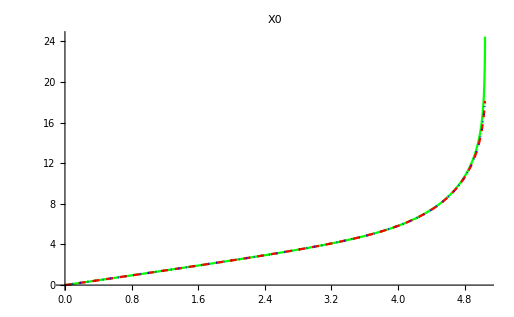

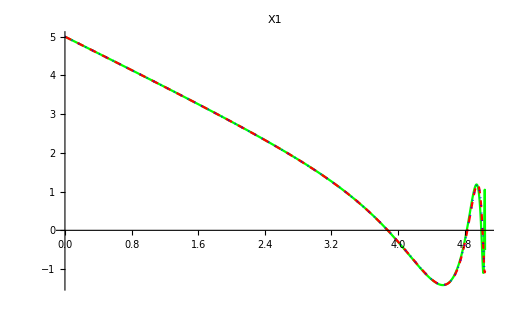

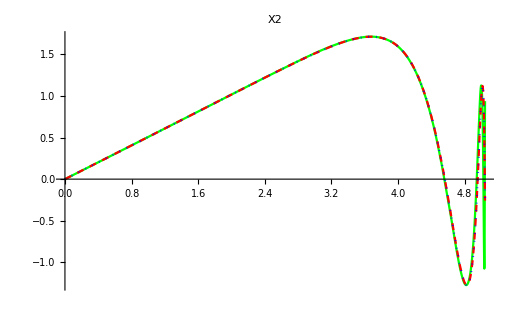

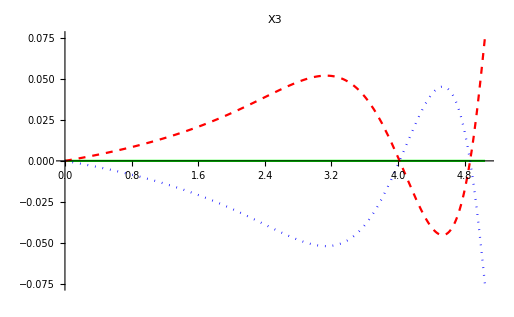

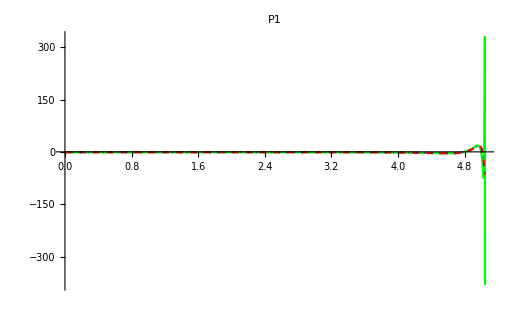

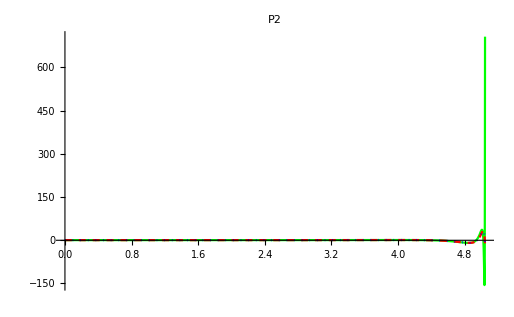

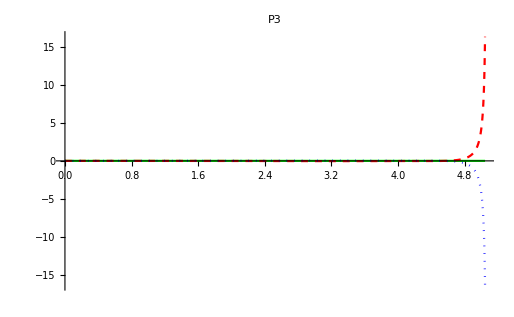

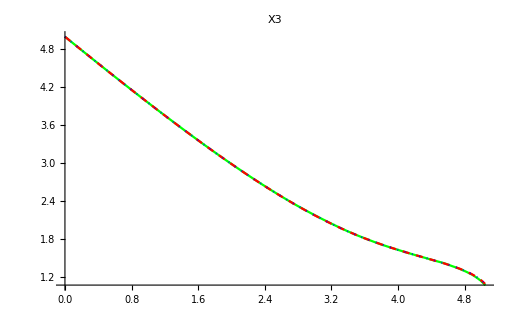

```mathematica
(* Plots *)

(* Plot range *)
range=5rs;
τplot0=Min[5.046,τint0,τmax];
τplot1=Min[5.046,τint1,τmax];
τplot2=Min[5.046,τint2,τmax];

(* 3D Plot *)
arrow1={Arrowheads[0.025],Arrow[Tube[{{-0.9range,-0.9range,0},{-0.9range+range/4,-0.9range,0}},0.2],-0]};
arrow2={Arrowheads[0.025],Arrow[Tube[{{-0.9range,-0.9range,0},{-0.9range,-0.9range+range/4,0}},0.2],-0]};
arrow3={Arrowheads[0.025],Arrow[Tube[{{-0.9range,-0.9range,0},{-0.9range,-0.9range,range/4}},0.2],-0]};
arrowtext1=Text[Style["x",Large,Bold],{-0.9range+range/3.5,-0.9range,0}];
arrowtext2=Text[Style["y",Large,Bold],{-0.9range,-0.9range+range/3.5,0}];
arrowtext3=Text[Style["z",Large,Bold],{-0.9range,-0.9range,range/3.5}];
frame=Graphics3D[{Yellow,arrow1,arrow2,arrow3,Black,arrowtext1,arrowtext2,arrowtext3}];
wall1=Graphics3D[{Transparent,EdgeForm[Thick],Polygon[{{-range,-range,-range},{-range,range,-range},{range,range,-range},{range,-range,-range}}]}];
wall2=Graphics3D[{Transparent,EdgeForm[Thick],Polygon[{{-range,range,-range},{-range,-range,-range},{-range,-range,range},{-range,range,range}}]}];
wall3=Graphics3D[{Transparent,EdgeForm[Thick],Polygon[{{-range,-range,-range},{-range,-range,range},{range,-range,range},{range,-range,-range}}]}];
source=Graphics3D[{Specularity[White,5],Orange,Sphere[{x1i ,x2i ,x3i },0.3rs]}];
plane=ContourPlot3D[z==0,{x,-range,range},{y,-range,range},{z,-range,range},Mesh->None,ContourStyle->Opacity[0.5]];
BH=Graphics3D[{Specularity[White,3],Black,Sphere[{0,0,0},M+√(M^2-a^2)]}];

g0=ParametricPlot3D[{Evaluate[(x1[τ])/.sol0][[1]],Evaluate[(x2[τ])/.sol0][[1]],Evaluate[(x3[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->{Thick,Green},PlotPoints->3000];
g1=ParametricPlot3D[{Evaluate[(x1[τ])/.sol1][[1]],Evaluate[(x2[τ])/.sol1][[1]],Evaluate[(x3[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Thick,Red},PlotPoints->3000];
g2=ParametricPlot3D[{Evaluate[(x1[τ])/.sol2][[1]],Evaluate[(x2[τ])/.sol2][[1]],Evaluate[(x3[τ])/.sol2][[1]]},{τ,0,τplot2},PlotStyle->{Thick,Blue},PlotPoints->3000];

Style[Show[g0,g1,g2,BH,source,plane,wall1,wall2,wall3,frame,PlotRange->{{-range,range},{-range,range},{-range,range}},Boxed->False,Axes->False,ViewPoint->{1.5,4,1.5}],Antialiasing->True]


(* Individual Plots *)

Show[Plot[{Evaluate[(x0[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"X0",PlotRange->All],Plot[{Evaluate[(x0[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"X0",PlotRange->All],Plot[{Evaluate[(x0[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"X0",PlotRange->All]]

Show[Plot[{Evaluate[(x1[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"X1",PlotRange->All],Plot[{Evaluate[(x1[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"X1",PlotRange->All],Plot[{Evaluate[(x1[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"X1",PlotRange->All]]

Show[Plot[{Evaluate[(x2[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"X2",PlotRange->All],Plot[{Evaluate[(x2[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"X2",PlotRange->All],Plot[{Evaluate[(x2[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"X2",PlotRange->All]]

Show[Plot[{Evaluate[(x3[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"X3",PlotRange->All],Plot[{Evaluate[(x3[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"X3",PlotRange->All],Plot[{Evaluate[(x3[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"X3",PlotRange->All]]

Show[Plot[{Evaluate[(p1[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"P1",PlotRange->All],Plot[{Evaluate[(p1[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"P1",PlotRange->All],Plot[{Evaluate[(p1[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"P1",PlotRange->All]]

Show[Plot[{Evaluate[(p2[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"P2",PlotRange->All],Plot[{Evaluate[(p2[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"P2",PlotRange->All],Plot[{Evaluate[(p2[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"P2",PlotRange->All]]

Show[Plot[{Evaluate[(p3[τ])/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"P3",PlotRange->All],Plot[{Evaluate[(p3[τ])/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"P3",PlotRange->All],Plot[{Evaluate[(p3[τ])/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"P3",PlotRange->All]]

Show[Plot[{Evaluate[(√(x1[τ]^2+x2[τ]^2+x3[τ]^2))/.sol0][[1]]},{τ,τ0,τplot0},PlotStyle->Green,PlotLegends->Automatic,PlotLabel->"X3",PlotRange->All],Plot[{Evaluate[(√(x1[τ]^2+x2[τ]^2+x3[τ]^2))/.sol1][[1]]},{τ,τ0,τplot1},PlotStyle->{Red,Dashed},PlotLegends->Automatic,PlotLabel->"X3",PlotRange->All],Plot[{Evaluate[(√(x1[τ]^2+x2[τ]^2+x3[τ]^2))/.sol2][[1]]},{τ,τ0,τplot2},PlotStyle->{Blue,Dotted},PlotLegends->Automatic,PlotLabel->"X3",PlotRange->All]]
```

```mathematica
(* Black hole shadows *)

Clear[a,s,ϵ];


(*  EOM *)
EOM0=EOM/.s->0;
EOM1=EOM/.s->-s;
EOM2=EOM;

(* Initial conditions *)
(* integration time τmax, small parameter/wavelength ϵ, Kerr parameter a  *)
τ0=0;
τmax=4 10^2;
ϵ=1/10;
a=0.99;

(* spin/polarization *)
s=1;

(* initial position *)
x0i=0;
x1i=10;
x2i=0;
x3i=0;

(* initial normalized momentum Pid *)
(* Pid=(-e0 + s1 e1 + s2 e2 + s3 e3), with s1^2 + s2^2 + s3^2 == 1 *)
Pid=(-e0+s1 e1+s2 e2+s3 e3)/.x->x1[τ]/.y->x2[τ]/.z->x3[τ]/.p1->p1[τ]/.p2->p2[τ]/.p3->p3[τ];;
p1i=Pid[[2]]/.τ->τ0;
p2i=Pid[[3]]/.τ->τ0;
p3i=Pid[[4]]/.τ->τ0;

(* initial data vector *)
id=(Xτ/.τ->τ0)=={x0i,x1i,x2i,x3i}&&(pτ/.τ->τ0)=={p1i,p2i,p3i};

(* stop if integration hits event horizon x1 = M + √(M^2 - a^2) (M == 1) or escapes at x1 = x1i + 4rs *)
τint=τmax;
horizon=WhenEvent[√(x1[τ]^2+x2[τ]^2+x3[τ]^2)≤M+√(M^2-a^2),Throw[√(x1[τ]^2+x2[τ]^2+x3[τ]^2)];"StopIntegration"];
escape=WhenEvent[√(x1[τ]^2+x2[τ]^2+x3[τ]^2)≥√(x1i^2+x2i^2+x3i^2)+rs,Throw[√(x1[τ]^2+x2[τ]^2+x3[τ]^2)];"StopIntegration"];

(* Integration *)
Sol0=ParametricNDSolveValue[EOM0&&id&&horizon&&escape,{},{τ,τ0,τmax},{s1,s2,s3},Method->{"EquationSimplification"->"Solve"}];
Sol1=ParametricNDSolveValue[EOM1&&id&&horizon&&escape,{},{τ,τ0,τmax},{s1,s2,s3},Method->{"EquationSimplification"->"Solve"}];
Sol2=ParametricNDSolveValue[EOM2&&id&&horizon&&escape,{},{τ,τ0,τmax},{s1,s2,s3},Method->{"EquationSimplification"->"Solve"}];


(* Shadow functions *)
shadow0[i1_,i2_]:=Catch[Sol0[-√(1-i1^2-i2^2),i1,i2]];
shadow1[i1_,i2_]:=Catch[Sol1[-√(1-i1^2-i2^2),i1,i2]];
shadow2[i1_,i2_]:=Catch[Sol2[-√(1-i1^2-i2^2),i1,i2]];
```

ParametricNDSolveValue::noout: No functions were specified for output from NDSolveValue.

```mathematica
(* Plot *)
kmax=0.6;
pl0=RegionPlot[If[1-i^2-j^2≥0,shadow0[j,i]<3rs,False],{i,-kmax,kmax},{j,-kmax,kmax},AspectRatio->1,PlotPoints->30,PlotStyle->None,BoundaryStyle->{Green,Thick}]//Quiet;
pl1=RegionPlot[If[1-i^2-j^2≥0,shadow1[j,i]<3rs,False],{i,-kmax,kmax},{j,-kmax,kmax},AspectRatio->1,PlotPoints->30,PlotStyle->None,BoundaryStyle->{Red,Thick}]//Quiet;
pl2=RegionPlot[If[1-i^2-j^2≥0,shadow2[j,i]<3rs,False],{i,-kmax,kmax},{j,-kmax,kmax},AspectRatio->1,PlotPoints->30,PlotStyle->None,BoundaryStyle->{Blue,Thick}]//Quiet;
Show[pl0,pl1,pl2,Axes->True,PlotRange->{{-kmax,kmax},{-kmax,kmax}},PlotLabel->Style["r = 10, θ = π/2, a = 0, ϵ = 0.9",20],FrameLabel->{Subscript[k, 2],Subscript[k, 3]},RotateLabel->False]
```

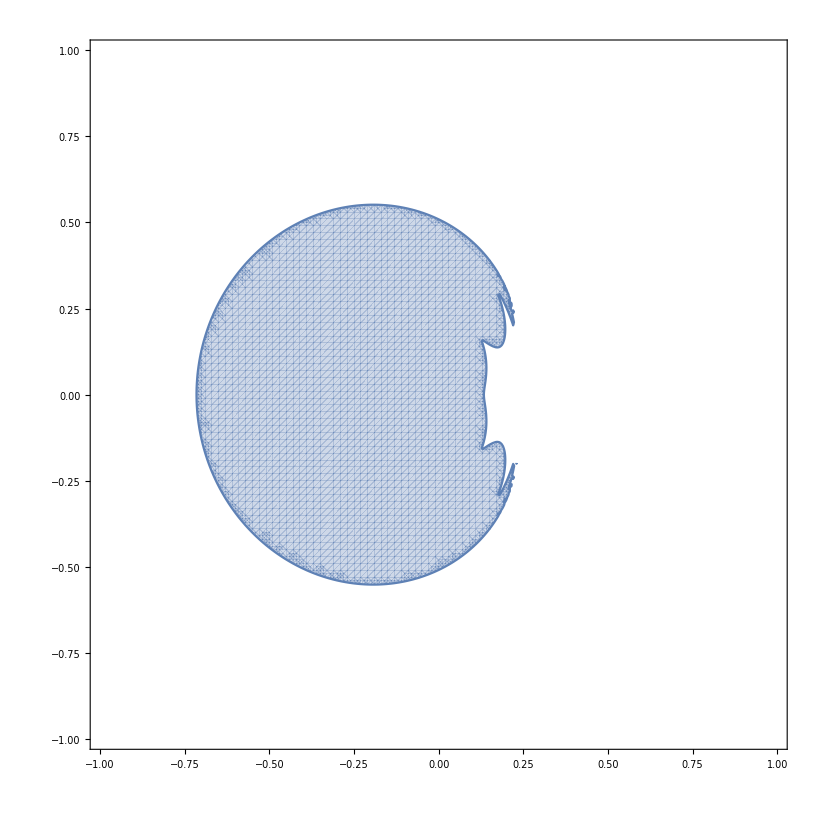

```mathematica
kmax=0.99;
RegionPlot[If[1-i^2-j^2≥0,shadow0[j,i]<3,False],{j,-kmax,kmax},{i,-kmax,kmax},AspectRatio->1,PlotPoints->100]
```

```mathematica
shadow0[i1_,i2_]:=Sol0[-√(1-i1^2-i2^2),i1,i2][Sol0[-√(1-i1^2-i2^2),i1,i2][[1]][[1]][[1]][[1]][[1]][[2]]];
```

```mathematica
shadow0[0,0]
```

1.14107

```mathematica
Catch[Sol0[-√(1-0.1^2-0.1^2),0.2,0.4]]
```

10.6603

```mathematica
Hold[Throw[10.660254037844386]]
```

Hold[Throw[10.6603]]

```mathematica
NDSolveValue[{y''[x]+y[x]==0,y[0]==0,y'[0]==1,WhenEvent[y[x]==0,Throw[y[x]];"StopIntegration"]},{},{x,∞}]//Quiet//Catch
```

1.45717×10^-16

```mathematica
Catch[Sol0[0.1,0.1,0.1]]
```

10.6603

```mathematica
Catch[Sol0[√(1-0.7^2-0.4^2),0.7,0.4]]
```

10.6603

```mathematica
N[√(x1i^2+x2i^2+x3i^2)+rs]
```

10.6603

```mathematica
r[x_,y_,z_]:=√((x^2+y^2+z^2-a^2+√((x^2+y^2+z^2-a^2)^2+4 a^2 z^2))/2);
```

```mathematica
ig/.a->0.99/.z->0.1/.x->0.1/.y->0.1//MatrixForm
```

(-1.20819 | 0.0229364 | -0.0186887 | 0.206077
0.0229364 | 0.997473 | 0.00205894 | -0.0227036
-0.0186887 | 0.00205894 | 0.998322 | 0.018499
0.206077 | -0.0227036 | 0.018499 | 0.796015)

```mathematica
g/.a->0.99/.z->0.1/.x->0.1/.y->0.1
```

{{-0.79181,0.0229364,-0.0186887,0.206077},{0.0229364,1.00253,-0.00205894,0.0227036},{-0.0186887,-0.00205894,1.00168,-0.018499},{0.206077,0.0227036,-0.018499,1.20399}}

```mathematica
pt0=(ig[[1]][[1]])^-1(-(∑_(i=2)^4 (ig[[1]][[i]]P[[i]]))+((∑_(i=2)^4 (ig[[1]][[i]]P[[i]]))^2-ig[[1]][[1]](∑_(i=2)^4 ∑_(j=2)^4 (ig[[i]][[j]]P[[i]]P[[j]])))^(1/2))//Simplify
```

-1/((a^2+r[x,y,z]^2) (a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4))(-2 p1 r[x,y,z]^3 (a y+x r[x,y,z])+2 p2 r[x,y,z]^3 (a x-y r[x,y,z])-2 p3 z r[x,y,z]^2 (a^2+r[x,y,z]^2)+(a^2+r[x,y,z]^2) (a^2 z^2+r[x,y,z]^4) √(1/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))(a^6 (p1^2+p2^2+p3^2) z^2-2 a^4 p3^2 z^2 r[x,y,z]+2 a^3 z (2 p2 p3 x-2 p1 p3 y+a p1^2 z+a p2^2 z+a p3^2 z) r[x,y,z]^2+2 a^2 (a^2 (p1^2+p2^2+p3^2)-p2^2 x^2-p1^2 y^2-2 p1 p3 x z-2 p3^2 z^2+2 p2 y (p1 x-p3 z)) r[x,y,z]^3+a (a^3 (p1^2+p2^2+p3^2)+a (p1^2+p2^2+p3^2) z^2+4 (p2 x-p1 y) (p1 x+p2 y+p3 z)) r[x,y,z]^4+(4 a^2 (p1^2+p2^2+p3^2)-2 (p1 x+p2 y+p3 z)^2) r[x,y,z]^5+2 a^2 (p1^2+p2^2+p3^2) r[x,y,z]^6+2 (p1^2+p2^2+p3^2) r[x,y,z]^7+(p1^2+p2^2+p3^2) r[x,y,z]^8)))

```mathematica
Clear[r]
```

```mathematica
P.ig.P//Simplify
```

1/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))(a^6 (-p0^2+p1^2+p2^2+p3^2) z^2-2 a^4 p3^2 z^2 r[x,y,z]+2 a^3 z (2 p3 (p2 x-p1 y)+a (2 p0 p3-p0^2 z+(p1^2+p2^2+p3^2) z)) r[x,y,z]^2-2 a^2 (a^2 p0^2+p2^2 x^2-2 p1 p2 x y+p1^2 y^2+2 a p0 (p2 x-p1 y)+2 p1 p3 x z+2 p2 p3 y z+2 p3^2 z^2) r[x,y,z]^3+a (a^3 (-p0^2+p1^2+p2^2+p3^2)+4 (p2 x-p1 y) (p1 x+p2 y+p3 z)+a (-p0^2 z^2+(p1^2+p2^2+p3^2) z^2+4 p0 (p1 x+p2 y+2 p3 z))) r[x,y,z]^4-2 (2 a^2 p0^2+2 a p0 (p2 x-p1 y)+(p1 x+p2 y+p3 z)^2) r[x,y,z]^5+(2 a^2 (-p0^2+p1^2+p2^2+p3^2)+4 p0 (p1 x+p2 y+p3 z)) r[x,y,z]^6-2 p0^2 r[x,y,z]^7+(-p0^2+p1^2+p2^2+p3^2) r[x,y,z]^8)

```mathematica
Solve[Simplify[P.ig.P]==0,p0][[2]][[1]][[2]]//Simplify
```

1/((a^2+r[x,y,z]^2)^2 (a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4))(2 a^4 p3 z r[x,y,z]^2+2 a^3 (-p2 x+p1 y) r[x,y,z]^3+2 a^2 (p1 x+p2 y+2 p3 z) r[x,y,z]^4+a (-2 p2 x+2 p1 y) r[x,y,z]^5+2 (p1 x+p2 y+p3 z) r[x,y,z]^6-√((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4) (a^6 (p1^2+p2^2+p3^2) z^2-2 a^4 p3^2 z^2 r[x,y,z]+2 a^3 z (2 p2 p3 x-2 p1 p3 y+a p1^2 z+a p2^2 z+a p3^2 z) r[x,y,z]^2+2 a^2 (a^2 (p1^2+p2^2+p3^2)-p2^2 x^2+2 p1 p2 x y-p1^2 y^2-2 p1 p3 x z-2 p2 p3 y z-2 p3^2 z^2) r[x,y,z]^3+a (a^3 (p1^2+p2^2+p3^2)+a (p1^2+p2^2+p3^2) z^2+4 (p2 x-p1 y) (p1 x+p2 y+p3 z)) r[x,y,z]^4+(4 a^2 (p1^2+p2^2+p3^2)-2 (p1 x+p2 y+p3 z)^2) r[x,y,z]^5+2 a^2 (p1^2+p2^2+p3^2) r[x,y,z]^6+2 (p1^2+p2^2+p3^2) r[x,y,z]^7+(p1^2+p2^2+p3^2) r[x,y,z]^8)))

```mathematica
(2 r[x,y,z]^2 (a^2+r[x,y,z]^2) (a^2 p3 z+a (-p2 x+p1 y) r[x,y,z]+(p1 x+p2 y+p3 z) r[x,y,z]^2)+√((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4) (a^6 (p1^2+p2^2+p3^2) z^2+r[x,y,z] (-2 a^4 p3^2 z^2+r[x,y,z] (2 a^3 z (2 p3 (p2 x-p1 y)+a (p1^2+p2^2+p3^2) z)+r[x,y,z] (2 a^2 (a^2 (p1^2+p2^2+p3^2)-(p2 x-p1 y)^2-2 p3 (p1 x+p2 y) z-2 p3^2 z^2)+r[x,y,z] (a (a^3 (p1^2+p2^2+p3^2)+a (p1^2+p2^2+p3^2) z^2+4 (p2 x-p1 y) (p1 x+p2 y+p3 z))+r[x,y,z] (4 a^2 (p1^2+p2^2+p3^2)-2 (p1 x+p2 y+p3 z)^2+(p1^2+p2^2+p3^2) r[x,y,z] (2 a^2+r[x,y,z] (2+r[x,y,z]))))))))))/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^3 (2+r[x,y,z])))-pt0//FullSimplify
```

1/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^3 (2+r[x,y,z])))(2 r[x,y,z]^2 (a^2+r[x,y,z]^2) (a^2 p3 z+a (-p2 x+p1 y) r[x,y,z]+(p1 x+p2 y+p3 z) r[x,y,z]^2)+√((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4) (a^6 (p1^2+p2^2+p3^2) z^2+r[x,y,z] (-2 a^4 p3^2 z^2+r[x,y,z] (2 a^3 z (2 p3 (p2 x-p1 y)+a (p1^2+p2^2+p3^2) z)+r[x,y,z] (2 a^2 (a^2 (p1^2+p2^2+p3^2)-(p2 x-p1 y)^2-2 p3 (p1 x+p2 y) z-2 p3^2 z^2)+r[x,y,z] (a (a^3 (p1^2+p2^2+p3^2)+a (p1^2+p2^2+p3^2) z^2+4 (p2 x-p1 y) (p1 x+p2 y+p3 z))+r[x,y,z] (4 a^2 (p1^2+p2^2+p3^2)-2 (p1 x+p2 y+p3 z)^2+(p1^2+p2^2+p3^2) r[x,y,z] (2 a^2+r[x,y,z] (2+r[x,y,z])))))))))+(a^2+r[x,y,z]^2) (-2 p1 r[x,y,z]^3 (a y+x r[x,y,z])+2 p2 r[x,y,z]^3 (a x-y r[x,y,z])-2 p3 z r[x,y,z]^2 (a^2+r[x,y,z]^2)+(a^2+r[x,y,z]^2) (a^2 z^2+r[x,y,z]^4) √(1/((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4))(a^6 (p1^2+p2^2+p3^2) z^2+r[x,y,z] (-2 a^4 p3^2 z^2+r[x,y,z] (2 a^3 z (2 p3 (p2 x-p1 y)+a (p1^2+p2^2+p3^2) z)+r[x,y,z] (2 a^2 (a^2 (p1^2+p2^2+p3^2)-(p2 x-p1 y)^2-2 p3 (p1 x+p2 y) z-2 p3^2 z^2)+r[x,y,z] (a (a^3 (p1^2+p2^2+p3^2)+a (p1^2+p2^2+p3^2) z^2+4 (p2 x-p1 y) (p1 x+p2 y+p3 z))+r[x,y,z] (4 a^2 (p1^2+p2^2+p3^2)-2 (p1 x+p2 y+p3 z)^2+(p1^2+p2^2+p3^2) r[x,y,z] (2 a^2+r[x,y,z] (2+r[x,y,z])))))))))))

```mathematica
Clear[r]
```

```mathematica
r[x_,y_,z_]:=√((x^2+y^2+z^2-a^2+√((x^2+y^2+z^2-a^2)^2+4 a^2 z^2))/2);
```

```mathematica
1/((a^2+r[x,y,z]^2)^2 (a^2 z^2+2 r[x,y,z]^3+r[x,y,z]^4))(2 a^4 p3 z r[x,y,z]^2+2 a^3 (-p2 x+p1 y) r[x,y,z]^3+2 a^2 (p1 x+p2 y+2 p3 z) r[x,y,z]^4+a (-2 p2 x+2 p1 y) r[x,y,z]^5+2 (p1 x+p2 y+p3 z) r[x,y,z]^6+√((a^2+r[x,y,z]^2)^2 (a^2 z^2+r[x,y,z]^4) (a^6 (p1^2+p2^2+p3^2) z^2-2 a^4 p3^2 z^2 r[x,y,z]+2 a^3 z (2 p2 p3 x-2 p1 p3 y+a p1^2 z+a p2^2 z+a p3^2 z) r[x,y,z]^2+2 a^2 (a^2 (p1^2+p2^2+p3^2)-p2^2 x^2+2 p1 p2 x y-p1^2 y^2-2 p1 p3 x z-2 p2 p3 y z-2 p3^2 z^2) r[x,y,z]^3+a (a^3 (p1^2+p2^2+p3^2)+a (p1^2+p2^2+p3^2) z^2+4 (p2 x-p1 y) (p1 x+p2 y+p3 z)) r[x,y,z]^4+(4 a^2 (p1^2+p2^2+p3^2)-2 (p1 x+p2 y+p3 z)^2) r[x,y,z]^5+2 a^2 (p1^2+p2^2+p3^2) r[x,y,z]^6+2 (p1^2+p2^2+p3^2) r[x,y,z]^7+(p1^2+p2^2+p3^2) r[x,y,z]^8)))/.a->0.99/.p1->1/.p2->2/.p3->1/.x->8/.y->0.1/.z->0.1
```

2.32425